```mathematica
(*resolucion de la acrecion como eq diferencial sola*)
```

```mathematica
f2[x_?NumericQ]:= σ*x^2*(1+x^2)^(-5/2)
```

```mathematica
mb := m0 * ab
Msol := 1989*10^(30) (*en gramos*)
m0 := 10^4*Msol 
m0 //N
ab := Rationalize[7.41*10^(-9), 0] (*adimensional*)
ηb := Rationalize[2.19*10^4,0]  (*en segundos*)
ηi := Rationalize[2.96*10^(12),0]   (*en segundos*)
G := 6.674*10^(-8)  (*en cgs*)
c := 2.998*10^(10)   (*en cgs*)
σ :=Rationalize[(81*G)/(8*c^3)*1/(ab*ηb), 0]
xi :=Rationalize[ηi/ηb, 0]
```

1.989×10^37

```mathematica
N[σ]
```

1.54534×10^-34

```mathematica
mx= NDSolve[{y'[x]==f2[x]*y[x]^2,y[0]==m0},y,{x,-10,20}, Method->{"StiffnessSwitching","NonstiffTest"->False},MaxSteps->Infinity,PrecisionGoal->20,WorkingPrecision->100]
```

NDSolve::ndsz: At x == 0.09968612005969604284839975401790752604574216787864319696548747210168756561367146146745456399683538521, step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[…]}}

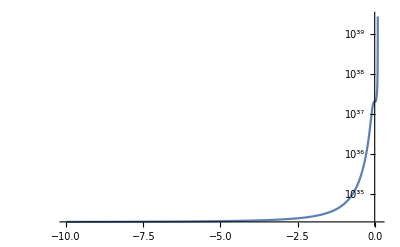

```mathematica
LogPlot[y[x]/.mx,{x,-10,10}, PlotRange->All]
```

```mathematica
a
```

```mathematica
mxm0= NDSolve[{y'[x]==m0*f2[x]*y[x]^2,y[0]==1},y,{x,-100,100}, Method->{"StiffnessSwitching","NonstiffTest"->False},MaxSteps->Infinity,PrecisionGoal->20,WorkingPrecision->100]
```

NDSolve::ndsz: At x == 0.09968612005969604284839975401790752604574216787864301696957929262818388714810237941245439670640679151, step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[…]}}

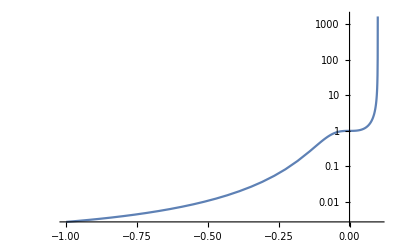

```mathematica
LogPlot[y[x]/.mxm0,{x,-1,1}, PlotRange->All]
```

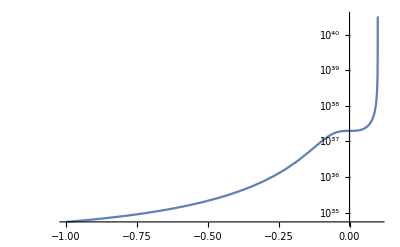

```mathematica
LogPlot[m0*y[x]/.mxm0,{x,-1,1}, PlotRange->All]
```

```mathematica
(* solucion analitica *)
```

```mathematica
g[x_]:=(σ*x^3)/(3*(x^2+1)^(3/2))
Man[x_] := (1/m0 -(g[x]-g[xi]))^(-1)
```

```mathematica
Plot[Man[x],{x,-10,10}, PlotRange->All]
```

-Graphics-

```mathematica
Man[0]
```

```mathematica
N[1/(1/19890000000000000000000000000000000000+12967168000000000000000000000000/(8504536615947464460186557301543383501554829007947639517 √876160000000000047961))]
```

1.93943×10^34

```mathematica
Plot[{Man[x],y[x]/.mx},{x,-10,10},PlotLegends->{"Analítica","Numérica"}]
```

-Graphics-

```mathematica
Mnum[x_]:= (y[x]/. First[mx])
```

```mathematica
Chop[ Mnum[10]- Man[10]]
```

InterpolatingFunction::dmval: Input value {10} lies outside the range of data in the interpolating function. Extrapolation will be used.

Power::infy: Infinite expression 1/0. encountered.

Power::indet: Indeterminate expression 0.^0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Power::indet: Indeterminate expression 0.^0. encountered.

3.×10^431-1/(1/19890000000000000000000000000000000000-500/(980366825934411367169773727190899097 √101)+12967168000000000000000000000000/(8504536615947464460186557301543383501554829007947639517 √876160000000000047961))

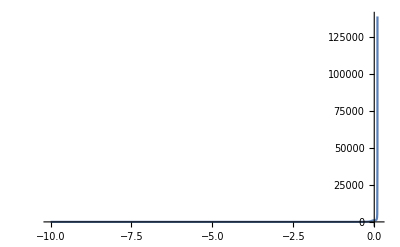

```mathematica
Plot[Abs[Man[x]-y[x]/.mx]/Man[x],{x,-10,10},PlotRange->All]
```

```mathematica
λ:= σ*m0
dudx= NDSolve[{y'[x]==λ*x^2*(1+x^2)^(-5/2)*y[x]^2,y[0]==1},y,{x,-100,100}, Method->{"StiffnessSwitching","NonstiffTest"->False},MaxSteps->Infinity,PrecisionGoal->20,WorkingPrecision->100]
```

NDSolve::ndsz: At x == 0.09968612005969604284839975401790752604574216787864301696957929262818388714810237941245439670640679151, step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[…]}}

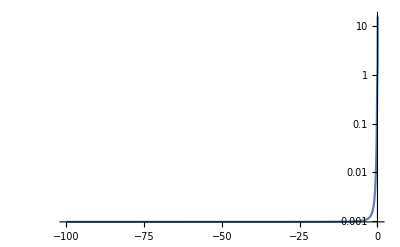

```mathematica
LogPlot[y[x]/.dudx,{x,-100,100}, PlotRange->All]
```

```mathematica
(*falta ver lo ultimo de chatgpt*)
```